```mathematica
Remove["Global`*"];
Unprotect[In,Out];
Clear[In,Out];
Off[General::spell1];
```

```mathematica
coords={t,r,θ,ϕ};
```

Define the metric

```mathematica
gdd={{g00,0,0,0},{0,g11,0,0},{0,0,g22,0},{0,0,0,g33}};
MatrixForm[gdd]
g00=-f[r];
g11=1/f[r];
g22=r^2;
g33=r^2 Sin[θ]^2;MatrixForm[gdd]
```

(g00 | 0 | 0 | 0
0 | g11 | 0 | 0
0 | 0 | g22 | 0
0 | 0 | 0 | g33)

(-f[r] | 0 | 0 | 0
0 | 1/f[r] | 0 | 0
0 | 0 | r^2 | 0
0 | 0 | 0 | r^2 Sin[θ]^2)

And its inverse and determinant

```mathematica
guu=Inverse[gdd];
dim=Length[gdd];
```

```mathematica
MatrixForm[guu]
```

(-1/f[r] | 0 | 0 | 0
0 | f[r] | 0 | 0
0 | 0 | 1/r^2 | 0
0 | 0 | 0 | Csc[θ]^2/r^2)

```mathematica
Do[g[i,j]=Simplify[gdd[[i,j]]];,{i,1,dim},{j,1,dim}];
Do[gu[i,j]=Simplify[guu[[i,j]]];,{i,1,dim},{j,1,dim}];
```

```mathematica
DET=Simplify[Det[gdd]];
minusg=Simplify[Sqrt[-DET],r>0&&Sin[θ]>0];
```

Define the tetrad and its inverse

```mathematica
euu={{e00,0,0,0},{0,e11,0,0},{0,0,e22,0},{0,0,0,e33}};
```

```mathematica
ut=1/Sqrt[-g00];
e00=ut;
e11=Sqrt[gu[2,2]];
e22=Sqrt[gu[3,3]];
e33=Sqrt[gu[4,4]];
edd=Simplify[Inverse[euu],Csc[θ]>0&&r>0&&f2[r,θ]>0&&f1[r,θ]>0&&f0[r,θ]>0&&H[r]>0];
dim=Length[gdd];
```

```mathematica
Do[e[i,j]=edd[[i,j]];,{i,1,dim},{j,1,dim}];
```

```mathematica
Do[eu[i,j]=euu[[i,j]];,{i,1,dim},{j,1,dim}];
```

```mathematica
Simplify[MatrixForm[edd],r>0&&Csc[θ]>0]
MatrixForm[euu]
```

(√f[r] | 0 | 0 | 0
0 | 1/(√f[r]) | 0 | 0
0 | 0 | r | 0
0 | 0 | 0 | r Sin[θ])

(1/(√f[r]) | 0 | 0 | 0
0 | √f[r] | 0 | 0
0 | 0 | √(1/r^2) | 0
0 | 0 | 0 | √(Csc[θ]^2/r^2))

Define the electromagnetic potential

```mathematica
A= 1/r^2{Q r,0,0,P Cos[θ] r^2};
MatrixForm[A]
```

(Q/r
0
0
P Cos[θ])

The electromagnetic tensor

```mathematica
F = Table[D[A[[ν]],coords[[μ]]] - D[A[[μ]],coords[[ν]]],{μ,1,dim},{ν,1,dim}];
MatrixForm[F]
```

(0 | Q/r^2 | 0 | 0
-Q/r^2 | 0 | 0 | 0
0 | 0 | 0 | -P Sin[θ]
0 | 0 | P Sin[θ] | 0)

and the EM tensor in the tetrad above

```mathematica
tetradF = Simplify[Table[Sum[F[[μ,ν]]euu[[b,μ]]euu[[c,ν]],{μ,1,dim},{ν,1,dim}],{b,1,dim},{c,1,dim}],r>0&&Csc[θ]>0];
MatrixForm[tetradF]
```

(0 | Q/r^2 | 0 | 0
-Q/r^2 | 0 | 0 | 0
0 | 0 | 0 | -P/r^2
0 | 0 | P/r^2 | 0)

Split it into the electric and magnetic fields

```mathematica
e1[r_,θ_] = Simplify[Re[tetradF[[1,2]]]];
e2[r_,θ_] = Simplify[Re[tetradF[[1,3]]]];
e3[r_,θ_] = Simplify[Re[tetradF[[1,4]]]];
b1[r_,θ_] = Simplify[Re[tetradF[[4,3]]]];
b2[r_,θ_] = Simplify[Re[tetradF[[2,4]]]];
b3[r_,θ_] = Simplify[Re[tetradF[[3,2]]]];
```

```mathematica
f[r_]:=1-(2M)/r+(Q^2+P^2)/r^2;
```

Coordinate transformations from the tetrad coordinates to Cartesian coordinates

```mathematica
x[r_,θ_,ϕ_]:=r Sin[θ] Cos[ϕ]
y[r_,θ_,ϕ_]:=r Sin[θ] Sin[ϕ]
z[r_,θ_,ϕ_]:=r Cos[θ]
```

Standard rules for transforming a vector field from spherical coordinates to Carteisan coordinates
https://en.wikipedia.org/wiki/Vector_fields_in_cylindrical_and_spherical_coordinates#Spherical_coordinate_system

```mathematica
ex[r_,θ_,ϕ_]:=e1[r,θ] Sin[θ] Cos[ϕ]+e2[r,θ] Cos[θ] Cos[ϕ]-e3[r,θ] Sin[ϕ]
ey[r_,θ_,ϕ_]:=e1[r,θ] Sin[θ] Sin[ϕ]+e2[r,θ] Cos[θ] Sin[ϕ]+e3[r,θ] Cos[ϕ]
ez[r_,θ_,ϕ_]:=e1[r,θ] Cos[θ]-e2[r,θ] Sin[θ]
```

```mathematica
bx[r_,θ_,ϕ_]:=b1[r,θ] Sin[θ] Cos[ϕ]+b2[r,θ] Cos[θ] Cos[ϕ]-b3[r,θ] Sin[ϕ]
by[r_,θ_,ϕ_]:=b1[r,θ] Sin[θ] Sin[ϕ]+b2[r,θ] Cos[θ] Sin[ϕ]+b3[r,θ] Cos[ϕ]
bz[r_,θ_,ϕ_]:=b1[r,θ] Cos[θ]-b2[r,θ] Sin[θ]
```

```mathematica
bx[r,θ,ϕ]
by[r,θ,ϕ]
bz[r,θ,ϕ]
```

Cos[ϕ] Re[P/r^2] Sin[θ]

Re[P/r^2] Sin[θ] Sin[ϕ]

Cos[θ] Re[P/r^2]

The parameters of the numerical solution and the corresponding event horizon radius

```mathematica
M=1;Q=0.;P=0.5;
```

```mathematica
rh = M+Sqrt[M^2-Q^2-P^2]
rMax=150;
```

1.86603

We start by looking at the YZ-plane.

```mathematica
ϕ=π/2;
```

We interpolate the functions ey and ez using the (y,z) coordinates and the same for by and bz.

```mathematica
bx[r,θ,ϕ]
by[r,θ,ϕ]
bz[r,θ,ϕ]
```

0.

0.5 Re[1/r^2] Sin[θ]

0.5 Cos[θ] Re[1/r^2]

```mathematica
r=.;θ=.;ϕ=.;
r[x_,y_,z_] := Sqrt[x^2+y^2+z^2];
θ[x_,y_,z_] := ArcCos[z/r[x,y,z]];
ϕ=π/2;
x=0;
```

```mathematica
YZby=Interpolation[Flatten[Table[{y,z,by[r[x,y,z],θ[x,y,z],ϕ]},{y,rh+0.01,rMax},{z,rh+0.01,rMax}],1],InterpolationOrder->1];
YZbz=Interpolation[Flatten[Table[{y,z,bz[r[x,y,z],θ[x,y,z],ϕ]},{y,rh+0.01,rMax},{z,rh+0.01,rMax}],1],InterpolationOrder->1];
```

```mathematica
YZb[y_,z_] = Sqrt[YZby[y,z]^2+YZbz[y,z]^2];
```

```mathematica
DYZb[y_,z_]=D[YZb[y,z],{{y,z}}];
```

```mathematica
cP=ContourPlot[YZb[y,z],{y,rh+0.01,rMax},{z,rh+0.01,rMax},Contours->8,ContourStyle->Red,ContourShading->Automatic,PlotLegends->Automatic,ColorFunction->"Pastel"];
```

```mathematica
sP=StreamPlot[DYZb[y,z],{y,rh+0.01,rMax},{z,rh+0.01,rMax},StreamPoints->Coarse,StreamStyle->Blue];
```

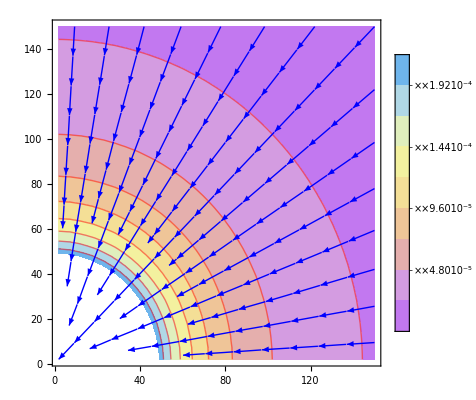

```mathematica
Show[cP,sP,AspectRatio->Automatic]
```

Now we restrict ourselves to the equatorial plane and do the same calculation.

```mathematica
ϕ=.;
```

```mathematica
θ=π/2;z=0;ϕ[x_,y_,z_] := ArcTan[y/x];x=.;
```

```mathematica
XYex=Interpolation[Flatten[Table[{x,y,ex[r[x,y,z],θ,ϕ[x,y,z]]},{x,rh+0.01,rMax},{y,rh+0.01,rMax}],1],InterpolationOrder->1];
XYey=Interpolation[Flatten[Table[{x,y,ey[r[x,y,z],θ,ϕ[x,y,z]]},{x,rh+0.01,rMax},{y,rh+0.01,rMax}],1],InterpolationOrder->1];
```

```mathematica
XYe[x_,y_]=Sqrt[XYex[x,y]^2+XYey[x,y]^2];
DXYe[x_,y_]=D[XYe[x,y],{{x,y}}];
```

```mathematica
XYeCP=ContourPlot[XYe[x,y],{x,rh+0.01,rMax},{y,rh+0.01,rMax},Contours->8,ContourStyle->Red,ContourShading->Automatic,PlotLegends->Automatic,ColorFunction->"Pastel"];
XYeSP=StreamPlot[DXYe[x,y],{x,rh+0.01,rMax},{y,rh+0.01,rMax},StreamPoints->Coarse,StreamStyle->{Blue,"Line"}];
```

Power::infy: Infinite expression 1/√0. encountered.

Infinity::indet: Indeterminate expression 0.\ √2\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/√0. encountered.

Infinity::indet: Indeterminate expression 0.\ √2\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/√0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0.\ √2\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {150., 1.88661} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

```mathematica
Show[XYeCP,XYeSP,AspectRatio->Automatic]
```

-Graphics-